```mathematica
rho[x_,y_]:=(Sin[(x+y)/2]/Sin[(x-y)/2])^2
sigma1[x_]:= (2/Sin[x])^(1/8)
sigma2[x_,y_]:=((rho[x,y]^(1/4)+rho[x,y]^(-1/4))^(1/2))/(4Sin[x]Sin[y])^(1/8)
sigma2c[x_,y_]:=sigma2[x,y]-sigma1[x]sigma1[y]
a= 0.0
```

0.

Power::infy: Infinite expression 1/0. encountered.

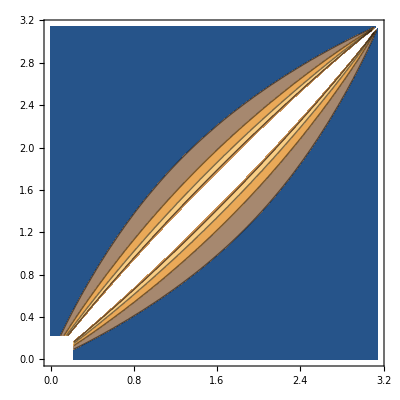

```mathematica
ContourPlot[sigma2c[x,y],{x,a,Pi-a},{y,a,Pi-a}]
```

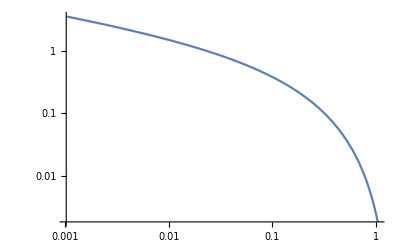

```mathematica
LogLogPlot[sigma2c[Pi/2-m,Pi/2+m],{m,0,Pi/3},PlotRange->All]
```

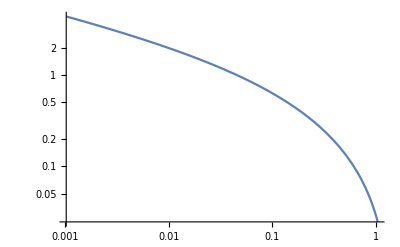

```mathematica
LogLogPlot[sigma2c[Pi/2,Pi/2+m],{m,0,Pi/3},PlotRange->All]
```

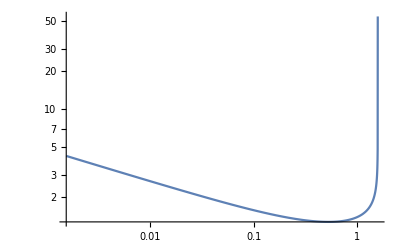

```mathematica
LogLogPlot[sigma2[Pi/2-m,Pi/2+m],{m,0,Pi/2},PlotRange->All]
```

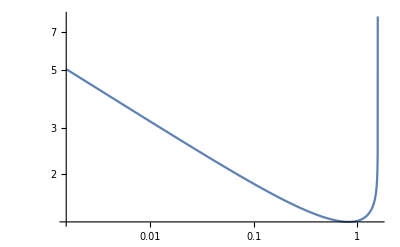

```mathematica
LogLogPlot[sigma2[Pi/2,Pi/2+m],{m,0,Pi/2},PlotRange->All]
```

```mathematica
Simplify[Series[sigma2[Pi/2-m,Pi/2+m],{m,0,3}],Assumptions->m>0]
```

1/(2^(1/4) m^(1/4))+m^(3/4)/(2 2^(1/4))+m^(7/4)/(24 2^(1/4))+m^(11/4)/(16 2^(1/4))+O[m]^(15/4)

```mathematica
Simplify[Series[sigma2c[Pi/2-m,Pi/2+m],{m,0,3}],Assumptions->m>0]
```

1/(2^(1/4) m^(1/4))-2^(1/4)+m^(3/4)/(2 2^(1/4))+m^(7/4)/(24 2^(1/4))-m^2/(4 2^(3/4))+m^(11/4)/(16 2^(1/4))+O[m]^(15/4)